# QEdark analysis for integrated form factors

v2: Updated June 14, 2019
Changes: 
- definition of electron mass and speed of light (me -> meeV, c -> ccms)
- fixed upper limit of GEout and SIout ((jj-3)binsize*10+shift -1 > (jj-3)binsize*10+shift)

The format of the C.*.dat files is the following:
There are 500 energy bins in 0.1 eV steps -- these correspond to columns 4-504. Column 3 is the sum of columns 4-504.

First line corresponds to December (Δv_earth = +15 km/s) for F_DM(q)=1. 
The second line to December for F_DM(q)~1/q. 
The third line to December for F_DM(q)~1/q^2.
The fourth line to March (Δv_earth = 0 km/s) for F_DM(q)~1.
The fifth line to March for F_DM(q)~1/q.
The sixth line to March for F_DM(q)~1/q^2.
The seventh line to June (Δv_earth = -15 km/s) for F_DM(q)=1.
The eight line to June for F_DM(q)~1/q.
The ninth line to June for F_DM(q)~1/q^2.

## User Inputs

set working directories

```mathematica
MyDirectory="My/Working/Directory/"; (* working directory where files are stored *)
PlotDir=MyDirectory<>"plots/";
```

bin sizing

```mathematica
Gebinsize = 2.9; (* choose Ge bin sizing in eV, 2.9 eV = 1 electron *)
Sibinsize=3.6; (* choose Si bin sizing in eV, 3.6 eV = 1 electron *)
```

```mathematica
GeShift=0.7*10; (* subtracts bandgap energy from Subscript[E, e]*)
SiShift=1.1*10; (* subtracts bandgap energy from Subscript[E, e]*)

SiEgap=1.1;
GeEgap=0.67;
```

exposure

```mathematica
nevents=3.0; (* events observed *)
years=1; (*exposure in years. 365.25 days = 1 year*)
kg=1.0; (* detector size in kg *)
```

choice of F_DM and time of year

```mathematica
FDMii=4; (* see below for indices *)
```

FDMii definitions:
1 = December (v_Earth=225 km/s) for F_DM(q) = 1.  
2 = December for F_DM(q) = αm_e/q. 
3 = December for F_DM(q) = (αm_e/q)^2.
4 = March (v_Earth=240km/s) for F_DM(q) = 1.  
5 = March forF_DM(q) = αm_e/q. 
6 = March for F_DM(q) = (αm_e/q)^2.
7 = June (v_Earth=255 km/s) for  F_DM(q) = 1.  
8 = June for F_DM(q) = αm_e/q. 
9 = June for F_DM(q) = (αm_e/q)^2.

## constants, definitions

Plot Options

```mathematica
Clear[PrettyExp]
PrettyExp[x_,MAX_: 2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
Clear[fticksR]
fticksR[min_,max_,AMAX_: 1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.005,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.015,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
Clear[fticksRNoLabels]
fticksRNoLabels[min_,max_,AMAX_: 1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.005,0}},{i,2,9}],{1}],{10.^x,"",{.015,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
```

```mathematica
DefaultPlotOptions =
  {ImageSize -> 350, AspectRatio->1.0, Frame -> True, Axes -> False, PlotRangePadding -> 0,
   TicksStyle -> Black, FrameTicksStyle -> Black, LabelStyle -> {(*Bold,*) Black, FontSize -> 18, FontFamily -> "Times"},
   FrameStyle -> Directive[Thickness[0.002]]};
```

```mathematica
SetOptions[Plot, DefaultPlotOptions];
 SetOptions[LogPlot, DefaultPlotOptions];
 SetOptions[LogLogPlot, DefaultPlotOptions];
 SetOptions[LogLinearPlot, DefaultPlotOptions];
 SetOptions[ListPlot, DefaultPlotOptions, Joined -> True];
 SetOptions[ListLogPlot, DefaultPlotOptions, Joined -> True];
 SetOptions[ListLogLinearPlot, DefaultPlotOptions, Joined -> True];
 SetOptions[ListLogLogPlot, DefaultPlotOptions, Joined -> True];
SetOptions[ListContourPlot,DefaultPlotOptions];

insetStyle={Black,FontSize->14,FontFamily->"Times"};
insetStyle2={Black,FontSize->14,FontFamily->"Times",Background->GrayLevel[0.9]};
lineStyle1={Black,AbsoluteThickness[1.3]};
lineStyle2={Black,AbsoluteThickness[1.1],Dashed,CapForm["Round"]};
QTicks[Qmax_]:=Join[Table[{n,n,0},{n,0,Qmax}],Table[{n,"",{0,0.01}},{n,0.51,Qmax}]];
GeEnergyTicks=With[{Egap=0.67,ε=2.9},Join[Table[{Q-0.485,Style[Round[#,If[#<1,0.01,0.1]]&[Egap +(Q-1)ε],10],0},{Q,0,15}],Table[{Q-0.485,"",{0.01,0}},{Q,0,15}]]];
SiEnergyTicks=With[{Egap=1.11,ε=3.6},Join[Table[{Q-0.485,Style[Round[#,If[#<1,0.01,0.1]]&[Egap +(Q-1)ε],10],0},{Q,0,12}],Table[{Q-0.485,"",{0.01,0}},{Q,0,12}]]];
style1000={Black,CapForm["Round"],AbsoluteThickness[2.2]};
style10={RGBColor[0.5,0.6,0.8],CapForm["Round"],AbsoluteThickness[2.0]};
myDashing=Dashing[{0.015,0.02}];
insetSize=14;
```

constants

```mathematica
a=2.6817268 10^-4; (* bohr radius [eV-1] *)
ccms=2.99792458 10^10;(*speed of light [cm/s]*)
vE=240.0 10^5 /ccms; (* average Earth velocity [cm/s] *)
v0=230.0 10^5/ccms;(* average DM velocity [cm/s] *)
vesc = 600.0 10^5/ccms;(* DM escape velocity [cm/s] *)
meeV=511. 10^3;(* electron mass [eV]*)
α=1/137.0;(* fine-structure constant *)
ρχ=0.4 10^9;(* local DM density [eV/cm^3]*)
sec2year=3600*24*365.25;
vcellSi=275.6154;
vcellGe=316.4269;(* bohr^3 *)
mGe=72.6; (* mass of Ge amu *)
mSi=28.09; (* mass of Si amu *)
amu2kg=1.66053904 10^-27;
McellGe=2*mGe amu2kg; (*2 atoms per unit cell*)
McellSi=2*mSi amu2kg; (*2 atoms per unit cell*)


QEtoSI=1/(10^5(2.68*^-4)^2); (* 10^5 to convert from (from [km/s])^-1 (to [cm/s])^-1, 2.68E-4 to convert from bohr^2 to eV^2*)
```

list of DM masses

```mathematica
mχ={1. 10^5,2. 10^5,2.25 10^5,2.5 10^5,2.75 10^5,3. 10^5,3.25 10^5,3.5 10^5,3.75 10^5,4. 10^5,4.25 10^5,4.5 10^5,4.75 10^5,5. 10^5,5.5 10^5,6. 10^5,6.5 10^5,7. 10^5,7.5 10^5,8. 10^5,9. 10^5,1. 10^6,2. 10^6,3. 10^6,4. 10^6,5. 10^6,6. 10^6,7. 10^6,8. 10^6,9. 10^6,1. 10^7,2. 10^7,5. 10^7,1. 10^8,2. 10^8,5. 10^8,1. 10^9, 1. 10^10};
iilist={"01","02","03","04","05","06","07","08","09","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38"};
```

prefactors

```mathematica
σtest=10^-37; (* reference cross-section in cm^2 *)
qfac=(α meeV 2.68*^-4); (* reference momentum q = Subscript[αm, e] in eV*)
For[ii=1,ii≤Length[mχ],ii++,
μχ[ii]=(mχ[[ii]]*meeV)/(mχ[[ii]]+meeV);
prefacGeσtest[ii]=ccms^2 vcellGe/McellGe ρχ/mχ[[ii]] σtest/μχ[ii]^2 1/(4π)1/(2 π)^3 QEtoSI sec2year;
prefacSiσtest[ii]=ccms^2 vcellSi/McellSi ρχ/mχ[[ii]] σtest/μχ[ii]^2 1/(4π)1/(2 π)^3 QEtoSI sec2year;
prefacGe[ii]=ccms^2 vcellGe/McellGe ρχ/mχ[[ii]] 1/μχ[ii]^2 1/(4π)1/(2 π)^3 QEtoSI sec2year;
prefacSi[ii]=ccms^2 vcellSi/McellSi ρχ/mχ[[ii]] 1/μχ[ii]^2 1/(4π)1/(2 π)^3 QEtoSI sec2year;
prefacGeFDMq[ii]=ccms^2 vcellGe/McellGe ρχ/mχ[[ii]] qfac^2/μχ[ii]^2 1/(4π)1/(2 π)^3 QEtoSI sec2year;
prefacSiFDMq[ii]=ccms^2 vcellSi/McellSi ρχ/mχ[[ii]] qfac^2/μχ[ii]^2 1/(4π)1/(2 π)^3 QEtoSI sec2year;
prefacGeFDMq2[ii]=ccms^2 vcellGe/McellGe ρχ/mχ[[ii]] qfac^4/μχ[ii]^2 1/(4π)1/(2 π)^3 QEtoSI sec2year;
prefacSiFDMq2[ii]=ccms^2 vcellSi/McellSi ρχ/mχ[[ii]] qfac^4/μχ[ii]^2 1/(4π)1/(2 π)^3 QEtoSI sec2year;]
```

```mathematica
FDMlist={"F","F","F(q) = (FractionBox[SubscriptBox[αm, e], q])","F","F","F(q) = (FractionBox[SubscriptBox[αm, e], q])","F","F","F(q) = (FractionBox[SubscriptBox[αm, e], q])"};
```

## Load input files

```mathematica
Clear[GEinValence,GEinSemicore,GEin,tmp]
Array[GEin,{Length[mχ]}];
Array[GEinValence,{Length[mχ]}];
Array[GEinSemicore,{Length[mχ]}];
Array[tmp,{Length[mχ]}];
For[ii=1,ii≤Length[mχ],ii++,
tmp=Import[MyDirectory<>"Ge243_GGA/SemicoreOnly/C."<>iilist[[ii]]<>".dat","table"];
GEinSemicore[ii]=tmp;
tmp=Import[MyDirectory<>"Ge243_GGA/ValenceOnly/C."<>iilist[[ii]]<>".dat","table"];
GEinValence[ii]=tmp;

GEin[ii]=GEinSemicore[ii]+GEinValence[ii];
 ]
```

```mathematica
Clear[SIin,tmp]
Array[SIin,{Length[mχ]}];
For[ii=1,ii≤Length[mχ],ii++,
tmp=Import[MyDirectory<>"Si243_GGA/C."<>iilist[[ii]]<>".dat","table"];
SIin[ii]=tmp]
```

```mathematica
numbins=Length[GEin[1][[1]]];
```

## E_R spectrum for (σ̄)_e=10^-37 cm^2

```mathematica
For[ii=1,ii≤Length[mχ],ii++,
GEout[ii]={};
For[jj=4,jj≤Floor[Length[GEin[1][[1]]]/(Gebinsize*10)],jj++,AppendTo[GEout[ii],{(jj-4)*Gebinsize+GeEgap,prefacGeσtest[ii]*Sum[GEin[ii][[FDMii,(ll+4)]],{ll,(jj-4)*Gebinsize*10+GeShift,(jj-3)Gebinsize*10+GeShift}]}]];

SIout[ii]={};
For[jj=4,jj≤Floor[Length[SIin[1][[1]]]/(Sibinsize*10)],jj++,AppendTo[SIout[ii],{(jj-4)*Sibinsize+SiEgap,prefacSiσtest[ii]*Sum[SIin[ii][[FDMii,(ll+4)]],{ll,(jj-4)*Sibinsize*10+SiShift,(jj-3)Sibinsize*10+SiShift}]}]];
]
```

```mathematica
For[ii=1,ii≤Length[mχ],ii++,
GEoutfunc[ii]=Interpolation[GEout[ii],InterpolationOrder->0];
SIoutfunc[ii]=Interpolation[SIout[ii],InterpolationOrder->0]
]
```

### plots of E_R spectra

InterpolatingFunction::dmval: Input value {0.000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

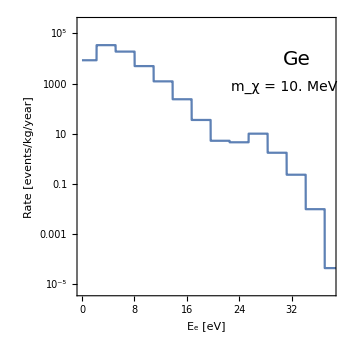

```mathematica
ii=31; (* sets the DM mass, 31 = 10 MeV *)
LogPlot[GEoutfunc[ii][x],{x,0,40},FrameLabel->{{"Rate [events/kg/year]",None},{"E_e [eV]","Q_th"}},FrameTicks->{Automatic,fticksR[10^-10,10^10,2],Table[{ii*Gebinsize+0.67,ToString[ii+1]},{ii,0,500}],fticksRNoLabels[10^-10,10^10,2]},PlotRange->{{0,38},All},
Epilog-> {Inset[Style["Ge",insetStyle,20],Scaled[{0.85,.85}]],Inset[Style["m_χ = "<>ToString[mχ[[ii]]/10^6]<>" MeV",insetStyle],Scaled[{0.8,.75}]]}]
```

InterpolatingFunction::dmval: Input value {0.000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

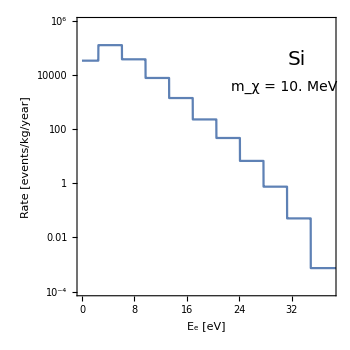

```mathematica
ii=31; (* sets the DM mass, 31 = 10 MeV *)
LogPlot[SIoutfunc[ii][x],{x,0.,40},FrameLabel->{{"Rate [events/kg/year]",None},{"E_e [eV]","Q_th"}},FrameTicks->{Automatic,fticksR[10^-10,10^10,2],Table[{ii*Sibinsize+1.1,ToString[ii+1]},{ii,0,500}],fticksRNoLabels[10^-10,10^10,2]},PlotRange->{{0,38},All},Epilog-> {Inset[Style["Si",insetStyle,20],Scaled[{0.85,.85}]],Inset[Style["m_χ = "<>ToString[mχ[[ii]]/10^6]<>" MeV",insetStyle],Scaled[{0.8,.75}]]}]
```

## (σ̄)_e vs. m_χ as a function of Q

create {m_χ, (σ̄)_e} tables as a function of Q

kk is index for number of electrons
ii is index for mass

```mathematica
Clear[GeAVGrate,SiAVGrate]
Array[GeAVGrate,20];
Array[SiAVGrate,20];
For[kk=1,kk≤20,kk++,
GeAVGrate[kk]={};
SiAVGrate[kk]={};

For[ii=1,ii≤Length[mχ],ii++,
AppendTo[GeAVGrate[kk],{mχ[[ii]]/10^6,nevents/years/kg/(prefacGe[ii]*Sum[GEin[ii][[FDMii,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}])}];
AppendTo[SiAVGrate[kk],{mχ[[ii]]/10^6,nevents/years/kg/(prefacSi[ii]*Sum[SIin[ii][[FDMii,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}])}];
];
]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

### print {m_χ, (σ̄)_e} for fixed Q

```mathematica
Q=1;
GeAVGrate[Q]
SiAVGrate[Q]
```

{{0.1,ComplexInfinity},{0.2,ComplexInfinity},{0.225,ComplexInfinity},{0.25,ComplexInfinity},{0.275,ComplexInfinity},{0.3,ComplexInfinity},{0.325,ComplexInfinity},{0.35,5.0713×10^-34},{0.375,8.08803×10^-35},{0.4,3.45671×10^-35},{0.425,4.96414×10^-36},{0.45,7.37412×10^-37},{0.475,2.66254×10^-37},{0.5,1.32713×10^-37},{0.55,5.13423×10^-38},{0.6,2.64476×10^-38},{0.65,1.61848×10^-38},{0.7,1.09255×10^-38},{0.75,7.84648×10^-39},{0.8,5.742×10^-39},{0.9,3.10395×10^-39},{1.,1.70035×10^-39},{2.,4.09822×10^-41},{3.,1.15322×10^-41},{4.,7.06521×10^-42},{5.,5.72508×10^-42},{6.,5.23131×10^-42},{7.,5.06805×10^-42},{8.,5.06391×10^-42},{9.,5.14728×10^-42},{10.,5.28348×10^-42},{20.,7.54784×10^-42},{50.,1.56276×10^-41},{100.,2.9398×10^-41},{200.,5.70354×10^-41},{500.,1.4002×10^-40},{1000.,2.7835×10^-40},{10000.,2.7684×10^-39}}

{{0.1,ComplexInfinity},{0.2,ComplexInfinity},{0.225,ComplexInfinity},{0.25,ComplexInfinity},{0.275,ComplexInfinity},{0.3,ComplexInfinity},{0.325,ComplexInfinity},{0.35,ComplexInfinity},{0.375,ComplexInfinity},{0.4,ComplexInfinity},{0.425,ComplexInfinity},{0.45,ComplexInfinity},{0.475,ComplexInfinity},{0.5,5.86666×10^-36},{0.55,1.33153×10^-37},{0.6,3.82115×10^-38},{0.65,1.67402×10^-38},{0.7,8.57156×10^-39},{0.75,4.97611×10^-39},{0.8,3.0696×10^-39},{0.9,1.33912×10^-39},{1.,6.65792×10^-40},{2.,1.56442×10^-41},{3.,4.19014×10^-42},{4.,2.46871×10^-42},{5.,1.94776×10^-42},{6.,1.74641×10^-42},{7.,1.66834×10^-42},{8.,1.6491×10^-42},{9.,1.66209×10^-42},{10.,1.69448×10^-42},{20.,2.35079×10^-42},{50.,4.80144×10^-42},{100.,9.0036×10^-42},{200.,1.74459×10^-41},{500.,4.28014×10^-41},{1000.,8.507×10^-41},{10000.,8.45942×10^-40}}

plots

User fixes the number of electrons, e.g. GeAVGrate[10] means a threshold of 10 electrons.

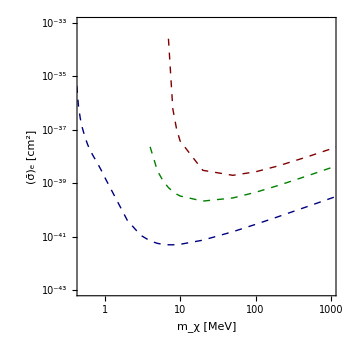

```mathematica
Gelimit=ListLogLogPlot[{GeAVGrate[10],GeAVGrate[5],GeAVGrate[1]},Joined->True,PlotRange->{{0.5,1000},{10^-43,10^-33}},PlotStyle->{{Dashed,Thick,Blend[{Red,Black}]},{Dashed,Thick,Blend[{Green,Black}]},{Dashed,Thick,Blend[{Blue,Black}]}},Frame->True,FrameLabel->{{"(σ̄)_e [cm^2]",None},{"m_χ [MeV]",FDMlist[[FDMii]]}},BaseStyle->FontSize->14,PlotMarkers->None,FrameTicks->{Automatic,fticksR[10^-45,10^-25,2],Automatic,fticksRNoLabels[10^-45,10^-25,2]}]
```

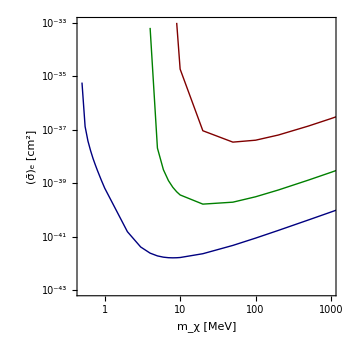

```mathematica
Silimit=ListLogLogPlot[{SiAVGrate[10],SiAVGrate[5],SiAVGrate[1]},Joined->True,PlotRange->{{0.5,1000},{10^-43,10^-33}},PlotStyle->{{Thick,Blend[{Red,Black}]},{Thick,Blend[{Green,Black}]},{Thick,Blend[{Blue,Black}]}},Frame->True,FrameLabel->{{"(σ̄)_e [cm^2]",None},{"m_χ [MeV]",FDMlist[[FDMii]]}},BaseStyle->FontSize->14,PlotMarkers->None,FrameTicks->{Automatic,fticksR[10^-45,10^-25,2],Automatic,fticksRNoLabels[10^-45,10^-25,2]}]
```

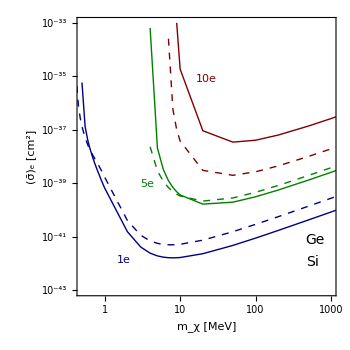

```mathematica
Show[Silimit,Gelimit,Epilog->{Inset[Style["1e",FontFamily->"Times",Blend[{Blue,Black}]],Scaled[{0.18,0.13}]],Inset[Style["5e",FontFamily->"Times",Blend[{Green,Black}]],Scaled[{0.27,0.4}]],Inset[Style["10e",FontFamily->"Times",Blend[{Red,Black}]],Scaled[{0.5,0.78}]],Inset[Style[""],Scaled[{0.82,0.2}]],
Inset[Style["Ge",insetStyle],Scaled[{0.92,0.2}]],Inset[Style[""],Scaled[{0.82,0.12}]],Inset[Style["Si",insetStyle],Scaled[{0.91,0.12}]]}]
```

## Annual modulation

```mathematica
modthick=0.008;
```

#### define functions

```mathematica
Clear[f1Si,fq2Si, σ1Si,σqSi, σq2Si]
Clear[f1Ge,fq2Ge, σ1Ge,σqGe, σq2Ge]
Σ=5;
B=0;
(* Si *)
f1Si[index_,kk_]:=1/(2 Sum[SIin[index][[4,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}])(Sum[SIin[index][[1,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}]-Sum[SIin[index][[7,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}]);
fqSi[index_,kk_]:=1/(2 Sum[SIin[index][[5,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}])(Sum[SIin[index][[2,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}]-Sum[SIin[index][[8,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}]);
fq2Si[index_,kk_]:=1/(2 Sum[SIin[index][[6,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}])(Sum[SIin[index][[3,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}]-Sum[SIin[index][[9,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}]);;
σ1Si[index_,kk_]:=1/(2 f1Si[index,kk]^2)(Σ^2+Σ √(Σ^2+4 f1Si[index,kk]^2 B))/(prefacSi[index]*Sum[SIin[index][[4,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}])
σq2Si[index_,kk_]:=1/(2 fq2Si[index,kk]^2)(Σ^2+Σ √(Σ^2+4 fq2Si[index,kk]^2 B))/(prefacSiFDMq[index]*Sum[SIin[index][[6,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}])
σqSi[index_,kk_]:=1/(2 fqSi[index,kk]^2)(Σ^2+Σ √(Σ^2+4 fqSi[index,kk]^2 B))/(prefacSiFDMq2[index]*Sum[SIin[index][[5,jj]],{jj,10.*Sibinsize(kk-1)+4+SiShift,numbins}])
(* Ge *)
f1Ge[index_,kk_]:=(1/(2 Sum[GEin[index][[4,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]))(Sum[GEin[index][[1,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]-Sum[GEin[index][[7,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]);
fqGe[index_,kk_]:=(1/(2 Sum[GEin[index][[5,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]))(Sum[GEin[index][[2,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]-Sum[GEin[index][[8,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]);
fq2Ge[index_,kk_]:=(1/(2 Sum[GEin[index][[6,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]))(Sum[GEin[index][[3,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]-Sum[GEin[index][[9,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}]);;
σ1Ge[index_,kk_]:=1/(2 f1Ge[index,kk]^2)(Σ^2+Σ √(Σ^2+4 f1Ge[index,kk]^2 B))/(prefacGe[index]*Sum[GEin[index][[4,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}])
σq2Ge[index_,kk_]:=1/(2 fq2Ge[index,kk]^2)(Σ^2+Σ √(Σ^2+4 fq2Ge[index,kk]^2 B))/(prefacGeFDMq[index]*Sum[GEin[index][[6,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}])
σqGe[index_,kk_]:=1/(2 fqGe[index,kk]^2)(Σ^2+Σ √(Σ^2+4 fqGe[index,kk]^2 B))/(prefacGeFDMq2[index]*Sum[GEin[index][[5,jj]],{jj,10.*Gebinsize(kk-1)+4+GeShift,numbins}])
```

#### create tables of {m_χ, (σ̄)_e} as a function of Q

```mathematica
For[kk=1,kk≤20,kk++,
ModFDM1Si[kk]={};
ModFDMqSi[kk]={};
ModFDMq2Si[kk]={};
AppendTo[ModFDM1Si[kk],Table[{mχ[[ii]]/10^6,σ1Si[ii,kk]},{ii,1,Length[mχ]}]];
AppendTo[ModFDMqSi[kk],Table[{mχ[[ii]]/10^6,σqSi[ii,kk]},{ii,1,Length[mχ]}]];
AppendTo[ModFDMq2Si[kk],Table[{mχ[[ii]]/10^6,σq2Si[ii,kk]},{ii,1,Length[mχ]}]];
ModFDM1Si[kk]=Flatten[ModFDM1Si[kk],1];
ModFDMqSi[kk]=Flatten[ModFDMqSi[kk],1];
ModFDMq2Si[kk]=Flatten[ModFDMq2Si[kk],1];

ModFDM1Ge[kk]={};
ModFDMqGe[kk]={};
ModFDMq2Ge[kk]={};
AppendTo[ModFDM1Ge[kk],Table[{mχ[[ii]]/10^6,σ1Ge[ii,kk]},{ii,1,Length[mχ]}]];
AppendTo[ModFDMqGe[kk],Table[{mχ[[ii]]/10^6,σqGe[ii,kk]},{ii,1,Length[mχ]}]];
AppendTo[ModFDMq2Ge[kk],Table[{mχ[[ii]]/10^6,σq2Ge[ii,kk]},{ii,1,Length[mχ]}]];
ModFDM1Ge[kk]=Flatten[ModFDM1Ge[kk],1];
ModFDMqGe[kk]=Flatten[ModFDMqGe[kk],1];
ModFDMq2Ge[kk]=Flatten[ModFDMq2Ge[kk],1];
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

#### FDM=1 plots

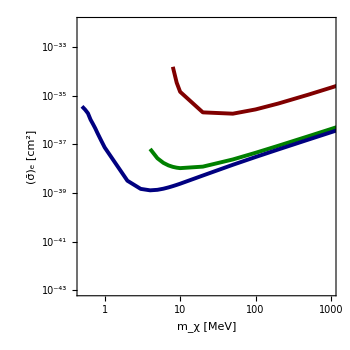

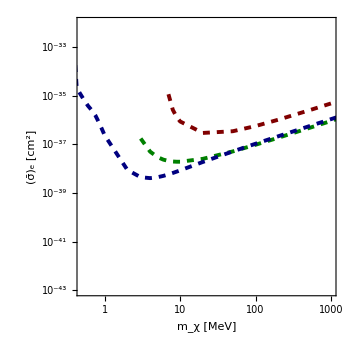

```mathematica
SiModFDM1plot=ListLogLogPlot[{ModFDM1Si[9],ModFDM1Si[4],ModFDM1Si[1]},Joined->True,PlotRange->{{0.5,1000},{10^-43,10^-32}},PlotStyle->{{Thickness[modthick],Blend[{Red,Black}]},{Thickness[modthick],Blend[{Green,Black}]},{Thickness[modthick],Blend[{Blue,Black}]}},Frame->True,FrameLabel->{{"(σ̄)_e [cm^2]",None},{"m_χ [MeV]","F_DM(q)=1"}},PlotMarkers->None,FrameTicks->{Automatic,fticksR[10^-45,10^-25,2],Automatic,fticksRNoLabels[10^-45,10^-25,2]}]
GeModFDM1plot=ListLogLogPlot[{ModFDM1Ge[9],ModFDM1Ge[4],ModFDM1Ge[1]},Joined->True,PlotRange->{{0.5,1000},{10^-43,10^-32}},PlotStyle->{{Dashed,Thickness[modthick],Blend[{Red,Black}]},{Dashed,Thickness[modthick],Blend[{Green,Black}]},{Dashed,Thickness[modthick],Blend[{Blue,Black}]}},Frame->True,FrameLabel->{{"(σ̄)_e [cm^2]",None},{"m_χ [MeV]","F_DM(q)=1"}},PlotMarkers->None,FrameTicks->{Automatic,fticksR[10^-45,10^-25,2],Automatic,fticksRNoLabels[10^-45,10^-25,2]}]
```

#### FDM=1/q plots

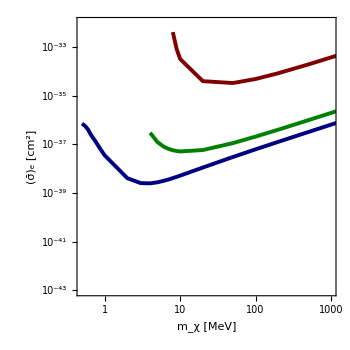

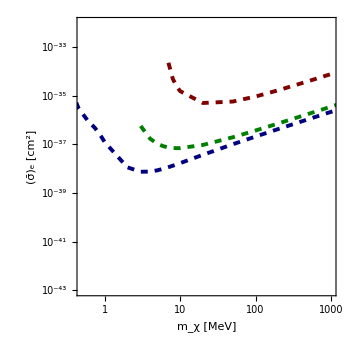

```mathematica
SiModFDMqplot=ListLogLogPlot[{ModFDMqSi[9],ModFDMqSi[4],ModFDMqSi[1]},Joined->True,PlotRange->{{0.5,1000},{10^-43,10^-32}},PlotStyle->{{Thickness[modthick],Blend[{Red,Black}]},{Thickness[modthick],Blend[{Green,Black}]},{Thickness[modthick],Blend[{Blue,Black}]}},Frame->True,FrameLabel->{{"(σ̄)_e [cm^2]",None},{"m_χ [MeV]","F_DM(q)=αm_e/q"}},PlotMarkers->None,FrameTicks->{Automatic,fticksR[10^-45,10^-25,2],Automatic,fticksRNoLabels[10^-45,10^-25,2]}]
GeModFDMqplot=ListLogLogPlot[{ModFDMqGe[9],ModFDMqGe[4],ModFDMqGe[1]},Joined->True,PlotRange->{{0.5,1000},{10^-43,10^-32}},PlotStyle->{{Dashed,Thickness[modthick],Blend[{Red,Black}]},{Dashed,Thickness[modthick],Blend[{Green,Black}]},{Dashed,Thickness[modthick],Blend[{Blue,Black}]}},Frame->True,FrameLabel->{{"(σ̄)_e [cm^2]",None},{"m_χ [MeV]","F_DM(q)=αm_e/q"}},PlotMarkers->None,FrameTicks->{Automatic,fticksR[10^-45,10^-25,2],Automatic,fticksRNoLabels[10^-45,10^-25,2]}]
```

#### FDM=1/q^2 plots

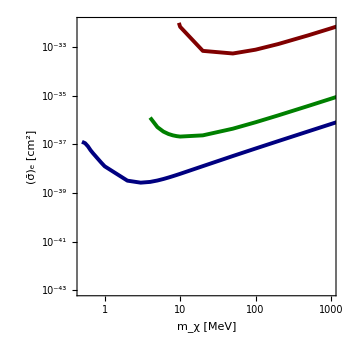

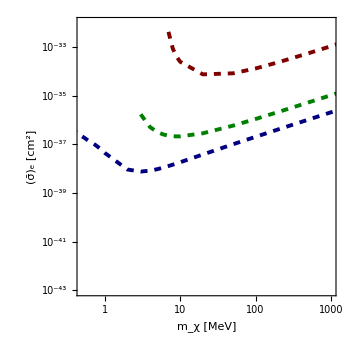

```mathematica
SiModFDMq2plot=ListLogLogPlot[{ModFDMq2Si[9],ModFDMq2Si[4],ModFDMq2Si[1]},Joined->True,PlotRange->{{0.5,1000},{10^-43,10^-32}},PlotStyle->{{Thickness[modthick],Blend[{Red,Black}]},{Thickness[modthick],Blend[{Green,Black}]},{Thickness[modthick],Blend[{Blue,Black}]}},Frame->True,FrameLabel->{{"(σ̄)_e [cm^2]",None},{"m_χ [MeV]","F_DM(q)=(αm_e/q)^2"}},PlotMarkers->None,FrameTicks->{Automatic,fticksR[10^-45,10^-25,2],Automatic,fticksRNoLabels[10^-45,10^-25,2]}]
GeModFDMq2plot=ListLogLogPlot[{ModFDMq2Ge[9],ModFDMq2Ge[4],ModFDMq2Ge[1]},Joined->True,PlotRange->{{0.5,1000},{10^-43,10^-32}},PlotStyle->{{Thickness[modthick],Dashed,Blend[{Red,Black}]},{Thickness[modthick],Dashed,Blend[{Green,Black}]},{Thickness[modthick],Dashed,Blend[{Blue,Black}]}},Frame->True,FrameLabel->{{"(σ̄)_e [cm^2]",None},{"m_χ [MeV]","F_DM(q)=(αm_e/q)^2"}},PlotMarkers->None,FrameTicks->{Automatic,fticksR[10^-45,10^-25,2],Automatic,fticksRNoLabels[10^-45,10^-25,2]}]
```